```mathematica
ClearAll["Global`*"]
```

```mathematica
Z0=50;
```

## Functions

```mathematica
SmithTran[z_]:=(z-Z0)/(z+Z0)
```

```mathematica
SmithTranInv[G_]:=-Z0(G+1)/(G-1)
```

```mathematica
ComplexSplit[v_]:=If[Length[v]==0,{Re[v],Im[v]},{Re[#],Im[#]}&/@v]
```

## Plot

### Parameters

```mathematica
sGridFineRefStep=0.25;
```

```mathematica
sGridThicknessCoarse=0.0015;
```

```mathematica
sGridThicknessFine=0.0005;
```

### Smith Chart Builder

```mathematica
sGridCoarse={0,1,2,5,10}//N;
sGridFine=Flatten[{Range[0,2,sGridFineRefStep],Range[2,5,sGridFineRefStep*2],Range[5,10,sGridFineRefStep*5]}]//N;
sGridFine=Complement[sGridFine,sGridCoarse](*remove from fine grid the ticks already declared in coarse one*);
sContoursCoarse={Re[SmithTranInv[x+I y]/Z0]==#&/@sGridCoarse,Im[SmithTranInv[x+I y]/Z0]==#&/@Flatten[{-sGridCoarse,sGridCoarse}]}//Flatten;
sContoursFine={Re[SmithTranInv[x+I y]/Z0]==#&/@sGridFine,Im[SmithTranInv[x+I y]/Z0]==#&/@Flatten[{-sGridFine,sGridFine}]}//Flatten;
sContourPlotArgument={sContoursCoarse,sContoursFine}//Flatten;
scGrid=ContourPlot[sContourPlotArgument//Evaluate,{x,-1,1},{y,-1,1},ContourStyle->Flatten[{ConstantArray[{Thickness->sGridThicknessCoarse,Black},sContoursCoarse//Length],ConstantArray[{Thickness->sGridThicknessFine,Lighter[Blue,0.5]},sContoursFine//Length]},1],ImageSize->Large];
```

```mathematica
scExclRegion=RegionPlot[x^2+y^2>1,{x,-1,1},{y,-1,1}];
```

```mathematica
scMainCircles=ContourPlot[{(x+0.5)^2+y^2==0.5^2,x^2+y^2==0.0005},{x,-1,1},{y,-1,1},ContourStyle->{{Black,Thickness->sGridThicknessCoarse}}];
```

```mathematica
exclRegion=RegionPlot[x^2+y^2>1,{x,-1,1},{y,-1,1}];
```

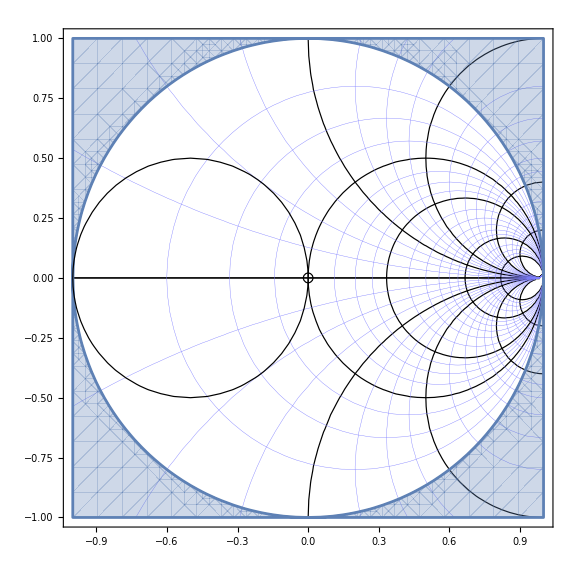

```mathematica
sc=Show[scGrid,exclRegion,scMainCircles]
```

### Plotting Function

```mathematica
scListPoint[z_]:=ListPlot[ComplexSplit[SmithTran[#]&/@z],PlotRange->{{-1,1},{-1,1}},AspectRatio->1,PlotStyle->Darker[Red,0.1]]
scCurve[zf_,FRange_]:=ParametricPlot[ComplexSplit[SmithTran[zf/.FREQUENCYvar->FREQUENCYvar]],{FREQUENCYvar,FRange[[1]],FRange[[2]]},PlotRange->{{-1,1},{-1,1}},AspectRatio->1,PlotStyle->Darker[Red,0.1],PlotPoints->100]
SmithChartListPlot[z_]:=Show[sc,scListPoint[z]]
SmithChartPlot[zf_,var_]:=Show[sc,scCurve[zf/.(var[[1]]->FREQUENCYvar),{var[[2]],var[[3]]}]]
```

```mathematica
par[a_,b_]:=a b/(a+b)
```